# Numerisk integrering

## Exempel från föreläsningen

### Exempel 1

Remove::rmnsm: There are no symbols matching "Global`*".

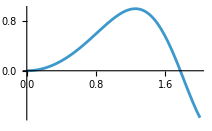

0.804428

0.804776

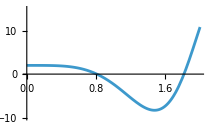

0.00288041

```mathematica
Remove["Global`*"]
f[x_]=Sin[x^2];
{a,b}={0,2};
Plot[f[x],{x,a,b}]
n=50;
h=(b-a)/n;
s=f[a];
For[i=1,i<n,++i,
xi=a+h*i;
s=s+2*f[xi];
]
s=s+f[b];
N[h*s/2]
(* Kontroll med Mathematica *)
NIntegrate[f[x],{x,0,2}]
(* Feluppskattning *)
d2f=FullSimplify[D[f[x],{x,2}]];
max=NMaxValue[{Abs[d2f],a≤x≤b},x];
Plot[d2f,{x,a,b},PlotRange->{-10,15}]
Abs[N[(b-a)^3/(12*n^2)]*max]
```

### Exempel 3

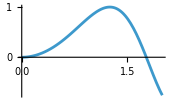

0.804777

0.804776

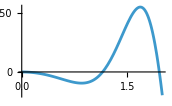

4.69162×10^-6

```mathematica
Remove["Global`*"]
f[x_]=Sin[x^2];
{a,b}={0,2};
Plot[f[x],{x,a,b}]
n=50;
h=(b-a)/n;
s=f[a];
For[i=1,i<n,i=i+1,
xi=a+h*i;
fact=2*2^Mod[i,2] (* faktorn är 4 för udda i och 2 för jämna i *);
s=s+fact*f[xi];
]
s=s+f[b];
N[h*s/3]
(* Kontroll med Mathematica *)
NIntegrate[f[x],{x,0,2}]
(* Feluppskattning *)
d4f=FullSimplify[D[f[x],{x,4}]];
max=NMaxValue[{Abs[d4f],a≤x≤b},x];
Plot[d4f,{x,a,b}]
Abs[N[(b-a)^5/(180*n^4)]*max ]
```

### Exempel 4

```mathematica
Remove["Global`*"]
{a,b}={0,2};
f[x_]=x^5-x;
n=3;
xi=NSolve[LegendreP[n,x]==0,x];
wi=2/(D[LegendreP[n,x],x]^2*(1-x^2))/.xi;
g=FullSimplify[(f[(a+b)/2+x*(b-a)/2]*(b-a)/2)]/.xi;
g.wi
NIntegrate[f[x],{x,a,b}]
```

8.66667

8.66667